```mathematica
ClearAll["`*"]
```

```mathematica
order = 3;
R = 10; Z=1; c = 137; k =-1
(*knot := Flatten[{0,0,0,Table[a,{a,1,9}],10,10,10}]*)
knot = Flatten[{0,0,0,Table[a,{a,0,2, 1/2}],3, 6, 9,12,15, 15, 15}]
n = Length[knot]-order-2
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
v=-Z/r;
```

-1

{0,0,0,0,1/2,1,3/2,2,3,6,9,12,15,15,15}

10

```mathematica
Cmat =  Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Cmat // Dimensions, SymmetricMatrixQ[Cmat]}
Cmat // MatrixForm
```

{{9,9},True}

(31/280 | 5/64 | 29/1680 | 1/6720 | 0 | 0 | 0 | 0 | 0
5/64 | 183/1120 | 283/2520 | 479/40320 | 1/13440 | 0 | 0 | 0 | 0
29/1680 | 283/2520 | 151/630 | 407/3360 | 817/90720 | 1/45360 | 0 | 0 | 0
1/6720 | 479/40320 | 407/3360 | 1265/4032 | 60707/362880 | 13619/1270080 | 1/11760 | 0 | 0
0 | 1/13440 | 817/90720 | 60707/362880 | 1955/3024 | 154927/423360 | 6287/105840 | 1/560 | 0
0 | 0 | 1/45360 | 13619/1270080 | 154927/423360 | 6085/7056 | 115307/211680 | 709/7840 | 3/3920
0 | 0 | 0 | 1/11760 | 6287/105840 | 115307/211680 | 2917853/2571912 | 773249/1143072 | 3084839/51438240
0 | 0 | 0 | 0 | 1/560 | 709/7840 | 773249/1143072 | 114523/102060 | 61/252
0 | 0 | 0 | 0 | 0 | 3/3920 | 3084839/51438240 | 61/252 | 155353/1837080)

```mathematica
Dmat =  Evaluate[Table[Integrate[ϕi[r,ai] D[ϕi[r,aj], r],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Dmat // Dimensions, SymmetricMatrixQ[Dmat]}
Dmat // MatrixForm
```

{{9,9},False}

(0 | 133/480 | 13/120 | 1/480 | 0 | 0 | 0 | 0 | 0
-133/480 | 0 | 109/360 | 223/2880 | 1/960 | 0 | 0 | 0 | 0
-13/120 | -109/360 | 0 | 259/720 | 77/1296 | 1/3240 | 0 | 0 | 0
-1/480 | -223/2880 | -259/720 | 0 | 10163/25920 | 4223/90720 | 1/1680 | 0 | 0
0 | -1/960 | -77/1296 | -10163/25920 | 0 | 10753/30240 | 1403/15120 | 1/240 | 0
0 | 0 | -1/3240 | -4223/90720 | -10753/30240 | 0 | 1313/4320 | 65/672 | 1/560
0 | 0 | 0 | -1/1680 | -1403/15120 | -1313/4320 | 8/6561 | 158429/489888 | 529357/7348320
0 | 0 | 0 | 0 | -1/240 | -65/672 | -144541/489888 | 961/5832 | 39457/174960
0 | 0 | 0 | 0 | 0 | -1/560 | -396077/7348320 | -2567/174960 | 14161/209952)

```mathematica
Vmat = Evaluate[Table[Integrate[ϕi[r,ai] v ϕi[r,aj], {r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Vmat // Dimensions, SymmetricMatrixQ[Vmat]}
Vmat // MatrixForm
```

{{9,9},True}

(1/60 (133-240 Log[2]) | (-3337+1440 Log[8])/1440 | 1/360 (319-480 Log[2]) | 1/480 (-111+160 Log[2]) | 0 | 0 | 0 | 0 | 0
(-3337+1440 Log[8])/1440 | 1/240 (2269+4320 Log[2]-4860 Log[3]) | (-15371+35640 Log[3/2]+1080 Log[2])/1080 | (77587-187920 Log[3/2]-2160 Log[2])/8640 | 1/576 (-1051+2592 Log[3/2]) | 0 | 0 | 0 | 0
1/360 (319-480 Log[2]) | (-15371+35640 Log[3/2]+1080 Log[2])/1080 | -2/27 (-737+726 Log[3/2]+3078 Log[2]-1536 Log[3]) | 1/720 (-49507+135680 Log[4/3]+25520 Log[3/2]+80 Log[2]) | (594569-1866240 Log[4/3]-142560 Log[3/2])/19440 | (-29827+103680 Log[4/3])/9720 | 0 | 0 | 0
1/480 (-111+160 Log[2]) | (77587-187920 Log[3/2]-2160 Log[2])/8640 | 1/720 (-49507+135680 Log[4/3]+25520 Log[3/2]+80 Log[2]) | 1/864 (113977-40368 ArcCoth[5]-269664 Log[4/3]+69960 Log[2]-69984 Log[3]) | (-6837581+12363840 Log[4/3]+8074080 Log[3/2])/77760 | (4645141-4808160 Log[4/3]-8048160 Log[3/2])/272160 | (-1051+2592 Log[3/2])/1008 | 0 | 0
0 | 1/576 (-1051+2592 Log[3/2]) | (594569-1866240 Log[4/3]-142560 Log[3/2])/19440 | (-6837581+12363840 Log[4/3]+8074080 Log[3/2])/77760 | 1/648 (54169-52488 Log[4/3]-79056 Log[3/2]-648 Log[65536]) | (-527033+163296 Log[4/3]+655776 Log[3/2]+305856 Log[2])/18144 | (230759-142560 Log[3/2]-250560 Log[2])/45360 | 1/240 (-111+160 Log[2]) | 0
0 | 0 | (-29827+103680 Log[4/3])/9720 | (4645141-4808160 Log[4/3]-8048160 Log[3/2])/272160 | (-527033+163296 Log[4/3]+655776 Log[3/2]+305856 Log[2])/18144 | (642019-1417176 ArcCoth[5]+228528 Log[2]-207360 Log[3]-21168 Log[4]+21168 Log[1/(131072 2^(149/196))])/21168 | (-15714391+32263920 Log[3/2]+3695760 Log[2])/635040 | (42309-100440 Log[3/2]-2360 Log[2])/3360 | 1/336 (-1051+2592 Log[3/2])
0 | 0 | 0 | (-1051+2592 Log[3/2])/1008 | (230759-142560 Log[3/2]-250560 Log[2])/45360 | (-15714391+32263920 Log[3/2]+3695760 Log[2])/635040 | (1669598539-5731864560 ArcCoth[5]+3149280 Log[2]+70421400 Log[3]-73570680 Log[6]+4389396480 Log[9]-4389396480 Log[10])/38578680 | (-314841649+1711342080 Log[10/9]+327233520 Log[3/2]+1691280 Log[2])/7348320 | (114246325-889636608 Log[10/9]-50668416 Log[3/2])/4408992
0 | 0 | 0 | 0 | 1/240 (-111+160 Log[2]) | (42309-100440 Log[3/2]-2360 Log[2])/3360 | (-314841649+1711342080 Log[10/9]+327233520 Log[3/2]+1691280 Log[2])/7348320 | (10661021-9340920 ArcCoth[5]-4860 Log[2]+83402460 Log[9]-83402460 Log[10])/174960 | (-48640619+433565460 Log[10/9]+7231680 Log[3/2])/1049760
0 | 0 | 0 | 0 | 0 | 1/336 (-1051+2592 Log[3/2]) | (114246325-889636608 Log[10/9]-50668416 Log[3/2])/4408992 | (-48640619+433565460 Log[10/9]+7231680 Log[3/2])/1049760 | (48390733-4478976 ArcCoth[5]+450775692 Log[9]-450775692 Log[10])/1259712)

```mathematica
Kmat = Evaluate[Table[Integrate[ϕi[r,ai] k/r ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Kmat // Dimensions, SymmetricMatrixQ[Kmat]}
Kmat // MatrixForm
```

{{9,9},True}

(1/60 (133-240 Log[2]) | (-3337+1440 Log[8])/1440 | 1/360 (319-480 Log[2]) | 1/480 (-111+160 Log[2]) | 0 | 0 | 0 | 0 | 0
(-3337+1440 Log[8])/1440 | 1/240 (2269+4320 Log[2]-4860 Log[3]) | (-15371+35640 Log[3/2]+1080 Log[2])/1080 | (77587-187920 Log[3/2]-2160 Log[2])/8640 | 1/576 (-1051+2592 Log[3/2]) | 0 | 0 | 0 | 0
1/360 (319-480 Log[2]) | (-15371+35640 Log[3/2]+1080 Log[2])/1080 | -2/27 (-737+726 Log[3/2]+3078 Log[2]-1536 Log[3]) | 1/720 (-49507+135680 Log[4/3]+25520 Log[3/2]+80 Log[2]) | (594569-1866240 Log[4/3]-142560 Log[3/2])/19440 | (-29827+103680 Log[4/3])/9720 | 0 | 0 | 0
1/480 (-111+160 Log[2]) | (77587-187920 Log[3/2]-2160 Log[2])/8640 | 1/720 (-49507+135680 Log[4/3]+25520 Log[3/2]+80 Log[2]) | 1/864 (113977-40368 ArcCoth[5]-269664 Log[4/3]+69960 Log[2]-69984 Log[3]) | (-6837581+12363840 Log[4/3]+8074080 Log[3/2])/77760 | (4645141-4808160 Log[4/3]-8048160 Log[3/2])/272160 | (-1051+2592 Log[3/2])/1008 | 0 | 0
0 | 1/576 (-1051+2592 Log[3/2]) | (594569-1866240 Log[4/3]-142560 Log[3/2])/19440 | (-6837581+12363840 Log[4/3]+8074080 Log[3/2])/77760 | 1/648 (54169-52488 Log[4/3]-79056 Log[3/2]-648 Log[65536]) | (-527033+163296 Log[4/3]+655776 Log[3/2]+305856 Log[2])/18144 | (230759-142560 Log[3/2]-250560 Log[2])/45360 | 1/240 (-111+160 Log[2]) | 0
0 | 0 | (-29827+103680 Log[4/3])/9720 | (4645141-4808160 Log[4/3]-8048160 Log[3/2])/272160 | (-527033+163296 Log[4/3]+655776 Log[3/2]+305856 Log[2])/18144 | (642019-1417176 ArcCoth[5]+228528 Log[2]-207360 Log[3]-21168 Log[4]+21168 Log[1/(131072 2^(149/196))])/21168 | (-15714391+32263920 Log[3/2]+3695760 Log[2])/635040 | (42309-100440 Log[3/2]-2360 Log[2])/3360 | 1/336 (-1051+2592 Log[3/2])
0 | 0 | 0 | (-1051+2592 Log[3/2])/1008 | (230759-142560 Log[3/2]-250560 Log[2])/45360 | (-15714391+32263920 Log[3/2]+3695760 Log[2])/635040 | (1669598539-5731864560 ArcCoth[5]+3149280 Log[2]+70421400 Log[3]-73570680 Log[6]+4389396480 Log[9]-4389396480 Log[10])/38578680 | (-314841649+1711342080 Log[10/9]+327233520 Log[3/2]+1691280 Log[2])/7348320 | (114246325-889636608 Log[10/9]-50668416 Log[3/2])/4408992
0 | 0 | 0 | 0 | 1/240 (-111+160 Log[2]) | (42309-100440 Log[3/2]-2360 Log[2])/3360 | (-314841649+1711342080 Log[10/9]+327233520 Log[3/2]+1691280 Log[2])/7348320 | (10661021-9340920 ArcCoth[5]-4860 Log[2]+83402460 Log[9]-83402460 Log[10])/174960 | (-48640619+433565460 Log[10/9]+7231680 Log[3/2])/1049760
0 | 0 | 0 | 0 | 0 | 1/336 (-1051+2592 Log[3/2]) | (114246325-889636608 Log[10/9]-50668416 Log[3/2])/4408992 | (-48640619+433565460 Log[10/9]+7231680 Log[3/2])/1049760 | (48390733-4478976 ArcCoth[5]+450775692 Log[9]-450775692 Log[10])/1259712)

```mathematica
Aprime = Table[If[k > 0, 
2 c^2 KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[i,2n-2],
c KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[j,2n-2]
],{i,1,2n-2},{j,1,2n-2}];
{Aprime // Dimensions, SymmetricMatrixQ[Aprime]}
Aprime // MatrixForm
```

{{18,18},True}

(137 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -137/2)

```mathematica
Amat = ArrayFlatten[{{Vmat, c (Dmat-Kmat)}, {-c(Dmat+Kmat), Vmat-2c^2 Cmat}}] + Aprime;
{Amat // Dimensions, SymmetricMatrixQ[Amat]}
N[Amat, 10] // MatrixForm
```

{{18,18},False}

(136.4440779 | -0.2379195694 | -0.03808512964 | -0.0002009398134 | 0 | 0 | 0 | 0 | 0 | 7.661321614 | 70.55539768 | 20.05932943 | 0.3129454211 | 0 | 0 | 0 | 0 | 0
-0.2379195694 | -0.3160829288 | -0.1589116593 | -0.01217604464 | -0.00005979129104 | 0 | 0 | 0 | 0 | -5.365435655 | 43.30336124 | 63.25145288 | 12.27610423 | 0.1508997402 | 0 | 0 | 0 | 0
-0.03808512964 | -0.1589116593 | -0.2523122115 | -0.09913205052 | -0.006064645284 | -0.00001262635796 | 0 | 0 | 0 | -9.624003907 | -19.70965823 | 34.56677298 | 62.86303537 | 8.970516898 | 0.04401376166 | 0 | 0 | 0
-0.0002009398134 | -0.01217604464 | -0.09913205052 | -0.2049904929 | -0.0896111788 | -0.004881312285 | -0.00003416645202 | 0 | 0 | -0.2578879122 | -8.939867995 | -35.70085352 | 28.08369753 | 65.99320526 | 7.046065621 | 0.08622842297 | 0 | 0
0 | -0.00005979129104 | -0.006064645284 | -0.0896111788 | -0.2652101443 | -0.1189460706 | -0.01585236713 | -0.0004018796267 | 0 | 0 | -0.1345169265 | -7.30880409 | -41.43974227 | 36.33378977 | 65.01125321 | 14.88414202 | 0.6258908422 | 0
0 | 0 | -0.00001262635796 | -0.004881312285 | -0.1189460706 | -0.2185275225 | -0.1114757577 | -0.0153996442 | -0.0001024993561 | 0 | 0 | -0.04055413958 | -5.708586055 | -32.42002986 | 29.93827059 | 56.91129918 | 15.36123935 | 0.2586852689
0 | 0 | 0 | -0.00003416645202 | -0.01585236713 | -0.1114757577 | -0.1860694008 | -0.09249521759 | -0.00692256599 | 0 | 0 | 0 | -0.07686681512 | -10.54059343 | -26.36694156 | 25.65855561 | 56.9774269 | 10.81757375
0 | 0 | 0 | 0 | -0.0004018796267 | -0.0153996442 | -0.09249521759 | -0.1336445864 | -0.0264295172 | 0 | 0 | 0 | 0 | -0.5157758245 | -11.14173684 | -27.74987811 | 40.88423976 | 34.51710014
0 | 0 | 0 | 0 | 0 | -0.0001024993561 | -0.00692256599 | -0.0264295172 | 68.49106097 | 0 | 0 | 0 | 0 | 0 | -0.2306004454 | -6.435956038 | 1.61079013 | 10.46512543
7.661321614 | -5.365435655 | -9.624003907 | -0.2578879122 | 0 | 0 | 0 | 0 | 0 | -4156.548779 | -2932.89417 | -648.0154661 | -5.586212845 | 0 | 0 | 0 | 0 | 0
70.55539768 | 43.30336124 | -19.70965823 | -8.939867995 | -0.1345169265 | 0 | 0 | 0 | 0 | -2932.89417 | -6133.757154 | -4215.735896 | -445.9621264 | -2.793065744 | 0 | 0 | 0 | 0
20.05932943 | 63.25145288 | 34.56677298 | -35.70085352 | -7.30880409 | -0.04055413958 | 0 | 0 | 0 | -648.0154661 | -4215.735896 | -8997.455487 | -4547.112823 | -338.0632295 | -0.8275699456 | 0 | 0 | 0
0.3129454211 | 12.27610423 | 62.86303537 | 28.08369753 | -41.43974227 | -5.708586055 | -0.07686681512 | 0 | 0 | -5.586212845 | -445.9621264 | -4547.112823 | -11777.38009 | -6279.904883 | -402.5228503 | -3.192040969 | 0 | 0
0 | 0.1508997402 | 8.970516898 | 65.99320526 | 36.33378977 | -32.42002986 | -10.54059343 | -0.5157758245 | 0 | 0 | -2.793065744 | -338.0632295 | -6279.904883 | -24268.3836 | -13737.00889 | -2229.809938 | -67.03254474 | 0
0 | 0 | 0.04401376166 | 7.046065621 | 65.01125321 | 29.93827059 | -26.36694156 | -11.14173684 | -0.2306004454 | 0 | 0 | -0.8275699456 | -402.5228503 | -13737.00889 | -32372.48752 | -20447.92972 | -3394.714634 | -28.72816372
0 | 0 | 0 | 0.08622842297 | 14.88414202 | 56.91129918 | 25.3244602 | -31.63373728 | -8.920790667 | 0 | 0 | 0 | -3.192040969 | -2229.809938 | -20447.92972 | -42587.32199 | -25393.26192 | -2251.224818
0 | 0 | 0 | 0 | 0.6258908422 | 15.36123935 | 53.09356773 | -4.265623071 | -27.27541243 | 0 | 0 | 0 | 0 | -67.03254474 | -3394.714634 | -25393.26192 | -42122.06559 | -9086.605795
0 | 0 | 0 | 0 | 0 | 0.2586852689 | 8.332739119 | 5.630897583 | -8.015832123 | 0 | 0 | 0 | 0 | 0 | -28.72816372 | -2251.224818 | -9086.605795 | -3242.916648)

```mathematica
Bmat = ArrayFlatten[{{Cmat,0}, {0,Cmat}}];
{Bmat // Dimensions, SymmetricMatrixQ[Bmat]}
```

{{18,18},True}

```mathematica
energy = Eigenvalues[N[{Amat, Bmat},30]]
```

{-41273.5700392054929379134606377,-37556.5221614370421167717441763,-37544.9300911259808356046656882,-37542.9897412304169239621555588,-37541.0365935669505128183965942,-37539.3637501123244026224823929,-37538.7064257029801499737566636,-37538.4117953035729128723429487,-37538.2117579660902982133708423,3736.47608708653167943613321804,2173.33980155637330667021617924,6.8186613770237754879846823421,3.24202537069159992712803536691,0.907319296601188055745801743629,-0.406258571988492928164843920952,0.298058315518794654000317487548,-0.107137321589606988857652656237,0.039265538796390159137857031815}

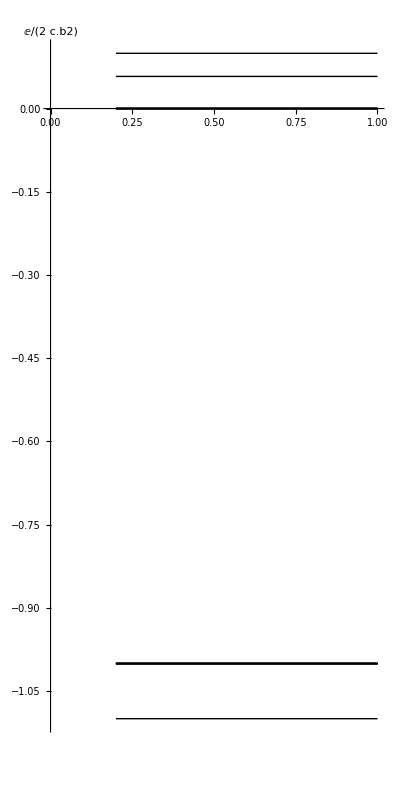

```mathematica
Plot[energy/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
```